x^2 y z^2

{4 x^3 y^2 z^4,2 x^4 y z^4,4 x^4 y^2 z^3}

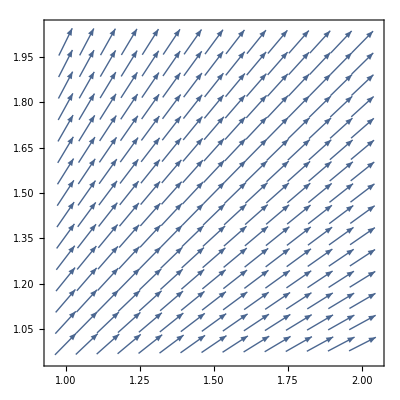

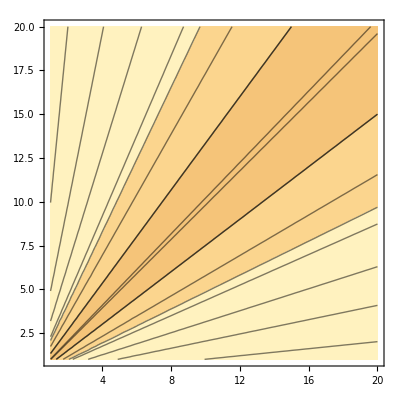

{x y,y,z^2}

a

{0,0,0}

b

Skalarprodukt a*b{x^3 y^2 z^2,x^2 y^2 z^2,x^2 y z^4}

Divergenz ab2 x^2 y z^2+3 x^2 y^2 z^2+4 x^2 y z^3

b mal nabla {x y ∇Null,y ∇Null,z^2 ∇Null}

{x y ∇Null,y ∇Null,z^2 ∇Null}

{{2 x^2 y z^2+3 x^2 y^2 z^2+2 x^3 y^4 z^2+4 x^2 y z^3,2 x^2 y z^2+3 x^2 y^2 z^2+2 x^4 y^3 z^2+4 x^2 y z^3,2 x^2 y z^2+3 x^2 y^2 z^2+4 x^2 y z^3},{2 x^2 y z^2+3 x^2 y^2 z^2+4 x^2 y z^3,2 x^2 y z^2+4 x^2 y^2 z^2+4 x^2 y z^3,2 x^2 y z^2+3 x^2 y^2 z^2+4 x^2 y z^3},{2 x^2 y z^2+3 x^2 y^2 z^2+4 x^2 y z^3,2 x^2 y z^2+3 x^2 y^2 z^2+4 x^2 y z^3,2 x^2 y z^2+3 x^2 y^2 z^2+4 x^2 y z^3+4 x^2 y z^6}}

c

Rot ab Rot[{x^3 y^2 z^2,x^2 y^2 z^2,x^2 y z^4}]

Rot bRot[{x y,y,z^2}]

-x^2 y z^2 Rot[{x y,y,z^2}]+Rot[{x^3 y^2 z^2,x^2 y^2 z^2,x^2 y z^4}]

Rot[{x (x+y+z),y (x+y+z),z (x+y+z)}]

```mathematica
skalar = (x^2*y*z^2)
nabla = Grad[skalar^2, {x,y,z}]

VectorPlot[{x/(Sqrt[x^2+y^2]), y/(Sqrt[x^2+y^2])}, {x,1,2}, {y,1,2}]
ContourPlot[f={x/(Sqrt[x^2+y^2]),  y/(Sqrt[x^2+y^2])}, {x,1,20}, {y,1,20}]
a = x^2*y*z^2;
b = {x*y,y,z^2}
Print["a"]
Grad[a^2,{x,y,z}] -2*a*Grad[a, {x,y,z}]
Print["b"]
ab = a*b;
Print["Skalarprodukt a*b",ab]
div = Div[ab, {x,y,z}] ;
Print["Divergenz ab",div]
bmalnabla = b*∇
Print["b mal nabla ",bmalnabla]
div+ (b*Grad[b,{x,y,z}])*(b*Grad[a,{x,y,z}])
Print["c"]
rotab = Rot[ab];
Print["Rot ab ", rotab]
Print["Rot b", Rot[b]]

Rot[ab] - a*Rot[b]
```

```mathematica
phi = x+y+z;
ä = {x,y,z};
Curl[phi*ä, {x,y,z}]
phi*(Curl[ä,{x,y,z}])+Cross[Grad[phi,{x,y,z}],ä]
```

{-y+z,x-z,-x+y}

{-y+z,x-z,-x+y}